The first step of the algorithm is to find the cohomology spaces whose dimensions are not equal to the number of A_1 singularities of f.  This can be done with Linear Algebra and is implemented through the code in this document.  Notation: Let P_j Ω^k be the set of all k-forms whose coefficients are homogeneous polynomials in ℂ[x_0,x_1,x_2,x_3] of degree j.  Let d be the degree of f, then A[f,n] is the matrix representation of the koszul differential df^:P_n Ω^3→P_(n+d-1)Ω^4, i.e., A[f,n] returns a 4(n+3
3)  by (n+d-1+3
3) matrix, where n is some positive integer.  Similarly the function B[f,n] is the matrix representation of df^:P_n Ω^2→P_(n+d-1)Ω^3 and therefore B[f,n] returns a 6(n+3
3) by 4(n+d-1+3
3) matrix.  Note that the 4 in 4(n+3
3) comes from the fact that there are four 3-forms dx_0^dx_1^dx_2, dx_0^dx_1^dx_3, dx_0^dx_2^dx_3, dx_1^dx_2^dx_3 and similarly the 6 in 6(n+3
3) is because there are six 2-forms dx_0^dx_1, dx_0^dx_2, dx_0^dx_3, dx_1^dx_2, dx_1^dx_3, dx_2^dx_3.  Here we are using the lexicographic order and this is the order we stick with throughout all computations.

```mathematica
allExp[n_]:=Module[{v={}},For[i=1,i≤Length[IntegerPartitions[n,4]],i++,
v=Append[v,Permutations[PadRight[IntegerPartitions[n,4][[i]],4]]]];
v=Reverse[Sort[ArrayFlatten[v,1]]]]
polyToVec[f_,list_]:=Module[{a=ConstantArray[0,Length[list]]},If[Depth[MonomialList[f,{Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]]==2,a=a,v=MonomialList[f,{Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}];
pos=Table[Position[list,Table[Exponent[v[[k]],Subscript[x, i]],{i,0,3}]][[1,1]],{k,1,Length[v]}];
coeff=v/.{Subscript[x, 0]->1,Subscript[x, 1]->1,Subscript[x, 2]->1,Subscript[x, 3]->1};
For[i=1,i≤Length[v],i++,
a=ReplacePart[a,pos[[i]]->coeff[[i]]]
]];a]
vecToPoly[v_,list_]:=Table[Total[Table[(∏_(j=0)^3 Subscript[x, j]^list[[Mod[k-1,Length[list]]+1,j+1]])v[[k]],{k,Length[list](m-1)+1,Length[list]m}]],{m,1,4}]
(* Assuming that f is homogeneous, this function finds the degree of f by finding the degree of the first monomial that appears in f. *)
homExp[f_]:=Total[Table[Exponent[MonomialList[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],{Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}][[1]],Subscript[x, i]],{i,0,3}]]
```

```mathematica
A[f_,n_]:=ArrayFlatten[Table[Table[polyToVec[(-1)^m(∏_(j=0)^3 Subscript[x, j]^(allExp[n][[k,j+1]]))D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, m]],allExp[n+homExp[f]-1]],{k,1,Length[allExp[n]]}],{m,3,0,-1}],1];
B[f_,n_]:=Module[{B={}},L=Length[allExp[n+homExp[f]-1]];B=Join[(*df^Subscript[dx, 0]^Subscript[dx, 1]*)Table[Join[polyToVec[(∏_(j=0)^3 Subscript[x, j]^(allExp[n][[k,j+1]]))D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 2]],allExp[n+homExp[f]-1]],polyToVec[(∏_(j=0)^3 Subscript[x, j]^(allExp[n][[k,j+1]]))D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 3]],allExp[n+homExp[f]-1]],ConstantArray[0,2L]],{k,1,Length[allExp[n]]}],(*df^Subscript[dx, 0]^Subscript[dx, 2]*)Table[Join[polyToVec[-(∏_(j=0)^3 Subscript[x, j]^(allExp[n][[k,j+1]]))D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 1]],allExp[n+homExp[f]-1]],ConstantArray[0,L],polyToVec[(∏_(j=0)^3 Subscript[x, j]^(allExp[n][[k,j+1]]))D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 3]],allExp[n+homExp[f]-1]],ConstantArray[0,L]],{k,1,Length[allExp[n]]}],(*df^Subscript[dx, 0]^Subscript[dx, 3]*)Table[Join[ConstantArray[0,L],polyToVec[-(∏_(j=0)^3 Subscript[x, j]^(allExp[n][[k,j+1]]))D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 1]],allExp[n+homExp[f]-1]],polyToVec[-(∏_(j=0)^3 Subscript[x, j]^(allExp[n][[k,j+1]]))D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 2]],allExp[n+homExp[f]-1]],ConstantArray[0,L]],{k,1,Length[allExp[n]]}],(*df^Subscript[dx, 1]^Subscript[dx, 2]*)Table[Join[polyToVec[(∏_(j=0)^3 Subscript[x, j]^(allExp[n][[k,j+1]]))D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 0]],allExp[n+homExp[f]-1]],ConstantArray[0,2L],polyToVec[(∏_(j=0)^3 Subscript[x, j]^(allExp[n][[k,j+1]]))D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 3]],allExp[n+homExp[f]-1]]],{k,1,Length[allExp[n]]}],(*df^Subscript[dx, 1]^Subscript[dx, 3]*)Table[Join[ConstantArray[0,L],polyToVec[(∏_(j=0)^3 Subscript[x, j]^(allExp[n][[k,j+1]]))D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 0]],allExp[n+homExp[f]-1]],ConstantArray[0,L],polyToVec[-(∏_(j=0)^3 Subscript[x, j]^(allExp[n][[k,j+1]]))D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 2]],allExp[n+homExp[f]-1]]],{k,1,Length[allExp[n]]}],(*df^Subscript[dx, 2]^Subscript[dx, 3]*)Table[Join[ConstantArray[0,2L],polyToVec[(∏_(j=0)^3 Subscript[x, j]^(allExp[n][[k,j+1]]))D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 0]],allExp[n+homExp[f]-1]],polyToVec[(∏_(j=0)^3 Subscript[x, j]^(allExp[n][[k,j+1]]))D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 1]],allExp[n+homExp[f]-1]]],{k,1,Length[allExp[n]]}]];B]
```

```mathematica
deRham[v_]:=-D[v[[1]],Subscript[x, 3]]+D[v[[2]],Subscript[x, 2]]-D[v[[3]],Subscript[x, 1]]+D[v[[4]],Subscript[x, 0]]
(* above is the de Rham differential for 3-forms ONLY. *)
(* koszul of a 3-form *)
koszul[v_]:=v[[4]]*D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 0]]-v[[3]]*D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 1]]+v[[2]]*D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 2]]-v[[1]]*D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 3]]
f[x0_,x1_,x2_,x3_]:=-3 x0^2 x1 x2+4 x0^2 x3^2-3 x0 x1^2 x2+4 x0 x1 x3^2+x1^2 x3^2-6 x1 x2 x3^2-3 x2^4
```

To get a better picture of the functions defined above let us consider the following example.

```mathematica
A[f,0]//MatrixForm
Dimensions[A[f,0]]
```

(0 | 0 | 0 | -8 | 0 | 0 | -8 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 12 | 0 | 0 | 0 | 0 | 0
0 | -3 | 0 | 0 | -3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6 | -12 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 6 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 6 | 0
0 | 0 | 0 | 0 | 0 | -6 | 0 | 0 | 0 | 8 | 0 | -3 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0)

{4,20}

The matrix A[f,0] represents the map df^:P_0 Ω^3→P_3 Ω^4 and has 4(0+3
3)=4 rows and (0+4-1+3
3)=6!/(3!3!)=20 columns.  The first row represents df^dx_0^dx_1^dx_2=-f_3dx_0^dx_1^dx_2^dx_3 where f_3=∂f/∂x_3.  The partial -f_3 is calculated below.

```mathematica
-D[f[Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[x, 3]]
```

-8 x_0^2 x_3-8 x_0 x_1 x_3-2 x_1^2 x_3+12 x_1 x_2 x_3

The non-zero coefficients of -f_3 are seen in the first row of A[f,0] and what column they are in is based off of the lexicographic ordering of monomials x_0>x_1>x_2>x_3.  With this ordering the first 4 monomials of degree 3 are x_0^3,x_0^2 x_1,x_0^2 x_2,x_0^2 x_3.  That is why there is a -8 in the first row, fourth column of A[f,0], to represent the term -8 x_0^2 x_3.  The second row of A[f,0] is df^dx_0^dx_1^dx_3=f_2 dx_0^dx_1^dx_2^dx_3 and so forth.  For A[f,1] the first row is df^(x_0 dx_0^dx_1^dx_2) and the matrix B[f,n] is constructed in the same way, however the first (n+d-1+3
3) columns represent the 3-form dx_0^dx_1^dx_2, the next  (n+d-1+3
3) columns represent the 3-form dx_0^dx_1^dx_3 and so on (the lexicographical ordering is always used).

Now since f=-3 x_0^2 x_1 x_2+4 x_0^2 x_3^2-3 x_0 x_1^2 x_2+4 x_0 x_1 x_3^2+x_1^2 x_3^2-6 x_1 x_2 x_3^2-3 x_2^4 is a quartic we are only interested in the modules P_j Ω^k where j+k is a multiple of 4.  The picture below shows these modules, where the map is the Koszul differential, df^.

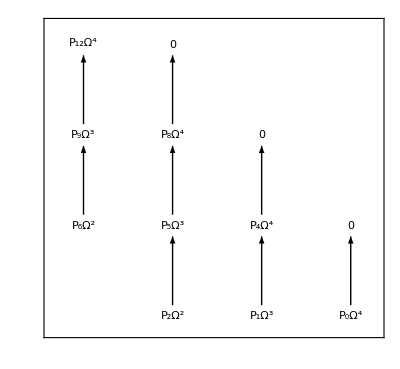

```mathematica
coor={{1,0},{0,0},{-1,0},{0,1},{-1,1},{-2,1},{-1,2},{-2,2},{-2,3.02},{1,1},{0,2},{-1,3}};
str={"P_0Ω^4","P_1Ω^3","P_2Ω^2","P_4Ω^4","P_5Ω^3","P_6Ω^2","P_8Ω^4","P_9Ω^3","P_12Ω^4","0","0","0"};
Graphics[{Table[Inset[Style[str[[k]],FontSize->Scaled[1/15],FontFamily->"Times New Roman"],coor[[k]]],{k,12}],Table[Arrow[{coor[[k]]+{0,0.12},coor[[k]]+{0,0.88}}],{k,8}]},PlotRange->{{-2.37,1.3},{-0.17,3.22}},Frame->True,FrameTicks->None]
```

By inspection dim(ker(P_0 Ω^4→0))=0 since the one basis element dx_0^dx_1^dx_2^dx_3 is sent to zero.  For dim(ker(P_1 Ω^3→P_4 Ω^4)) we must call on Mathematica’s NullSpace[] and Transpose[] functions.  Note that by the definition of A[f,n] and B[f,n] multiplication is defined on the left so this is why we need the Transpose[] function.

```mathematica
Length[NullSpace[Transpose[A[f,1]]]]
```

0

Hence dim(ker(P_1 Ω^3→P_4 Ω^4))=0.  Now for the dimensions of the other spaces.

```mathematica
{Length[NullSpace[Transpose[A[f,5]]]]-MatrixRank[B[f,2]],Binomial[3+4,3]-MatrixRank[A[f,1]]}
{Length[NullSpace[Transpose[A[f,9]]]]-MatrixRank[B[f,6]],Binomial[3+8,3]-MatrixRank[A[f,5]]}
```

{5,19}

{6,6}

We now have the dimensions of all six spaces mentioned in step 1 of the algorithm and display them in the E_1 page below.

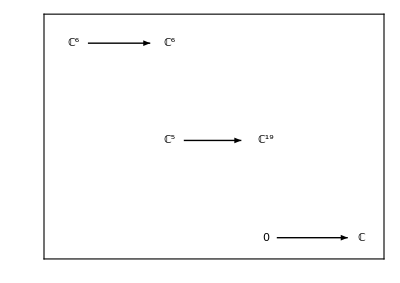

```mathematica
strE1={"ℂ","0","ℂ^19","ℂ^5","ℂ^6","ℂ^6"};
coorE1={{1,0},{0,0},{0,1},{-1,1},{-1,2},{-2,2}};
Graphics[{Table[Inset[Style[strE1[[k]],FontSize->Scaled[1/12],FontFamily->"Times New Roman"],coorE1[[k]]],{k,6}],{Arrow[{{0.12,0},{0.86,0}}]},{Arrow[{{-0.85,1},{-0.25,1}}]},{Arrow[{{-1.85,2},{-1.2,2}}]}},PlotRange->{{-2.24,1.17},{-0.17,2.25}},Frame->True,FrameTicks->None]
```

Since dim((H^3(K_f^●))_9)=dim((H^4(K_f^●))_8)=6= #Sing(f) we do not have to find bases for these spaces.  Moving down one “level” we have dim((H^3(K_f^●))_5)=5 and dim((H^4(K_f^●))_4)=19 so we must find bases for these spaces.  The simplest way to do this is to add the rows of NullSpace[Transpose[A[f,5]]] to B[f,2] and see if they increase the rank of the resulting matrix.  The following code shows how this can be done.

```mathematica
MatrixRank[B[f,2]]
N5=NullSpace[Transpose[A[f,5]]];
MatrixRank[Join[{N5[[1]],N5[[2]],N5[[3]],N5[[5]],N5[[6]]},B[f,2]]]
```

60

65

These 5 elements give us a basis for (H^3(K_f^●))_5 but computationally we can do better because these 3-forms are too “big.”  To see why, let {h_1,h_2,h_3,h_4}=h_1 dx_0^dx_1^dx_2+h_2 dx_0^dx_1^dx_3+h_3 dx_0^dx_2^dx_3+h_4 dx_1^dx_2^dx_3, then the following 3-form is an element of (H^3(K_f^●))_5=ker(P_5 Ω^3→P_8 Ω^4)/im(P_2 Ω^2→P_5 Ω^3).

```mathematica
vecToPoly[N5[[1]],allExp[5]]
```

{-4160 x_0^4 x_3-5244 x_0^3 x_1 x_3+988 x_0^2 x_1^2 x_3+534 x_0 x_1^3 x_3+4 x_1^4 x_3-354 x_0^3 x_2 x_3-297 x_0^2 x_1 x_2 x_3+72 x_0 x_1^2 x_2 x_3+12 x_1^3 x_2 x_3-144 x_0^2 x_2^2 x_3-144 x_0 x_1 x_2^2 x_3+72 x_1^2 x_2^2 x_3-8752 x_0^2 x_3^3-2384 x_0 x_1 x_3^3+146 x_1^2 x_3^3-708 x_0 x_2 x_3^3-210 x_1 x_2 x_3^3-288 x_2^2 x_3^3-432 x_3^5,-288 x_0^3 x_3^2-432 x_0^2 x_1 x_3^2+72 x_1^3 x_3^2-576 x_0 x_3^4-288 x_1 x_3^4,-8320 x_0^4 x_1-10704 x_0^3 x_1^2-4588 x_0^2 x_1^3-666 x_0 x_1^4-4 x_1^5+900 x_0^3 x_1 x_2+450 x_0^2 x_1^2 x_2+576 x_0^2 x_1 x_2^2+288 x_0 x_1^2 x_2^2-2144 x_0^3 x_3^2+14384 x_0^2 x_1 x_3^2+2956 x_0 x_1^2 x_3^2-362 x_1^3 x_3^2-1152 x_0^2 x_2 x_3^2-1152 x_0 x_2^2 x_3^2+864 x_0 x_3^4+1296 x_1 x_3^4,-4160 x_0^5-11592 x_0^4 x_1-7202 x_0^3 x_1^2-1320 x_0^2 x_1^3-8 x_0 x_1^4+450 x_0^4 x_2+900 x_0^3 x_1 x_2+288 x_0^3 x_2^2+576 x_0^2 x_1 x_2^2-9824 x_0^3 x_3^2-648 x_2 x_3^4}

The following 3-form is also in (H^3(K_f^●))_5 and it has fewer terms with smaller coefficients (in ℤ) than the 3-form above. 
-x_0^2(x_3(2 x_0^2+2 x_0 x_1-x_1^2+4 x_3))^2 dx_0^dx_1^dx_2-x_0^2(4 x_0^2 x_1+x_0(4 x_1^2-6 x_1 x_2+8 x_3^2)+x_1(x_1^2-3 x_1 x_2-4 x_3^2))dx_0^dx_2^dx_3)+x_0^2(-2 x_0^3+x_0^2(-5 x_1+3 x_2)+6 x_2 x_3^2-2x_0(x_1^2-3 x_1 x_2+4 x_3^2))dx_0^dx_2^dx_3

We now explain where this 3-form comes from.  First let us find the smallest j such that ker(P_j Ω^3→P_(j+3)Ω^4)≠0.

```mathematica
Table[Length[NullSpace[Transpose[A[f,k]]]],{k,0,3}]
```

{0,0,0,7}

Hence ker(P_j Ω^3→P_(j+3)Ω^4)=0 for j=0,1,2 and ker(P_3 Ω^3→P_6 Ω^4)≠0.

```mathematica
n1=NullSpace[Transpose[A[f,3]]][[1]];
vecToPoly[n1,allExp[3]]
MatrixRank[B[f,0]]
MatrixRank[Join[{n1},B[f,0]]]
```

{-2 x_0^2 x_3-2 x_0 x_1 x_3+x_1^2 x_3-4 x_3^3,0,-4 x_0^2 x_1-4 x_0 x_1^2-x_1^3+6 x_0 x_1 x_2+3 x_1^2 x_2-8 x_0 x_3^2+4 x_1 x_3^2,-2 x_0^3-5 x_0^2 x_1-2 x_0 x_1^2+3 x_0^2 x_2+6 x_0 x_1 x_2-8 x_0 x_3^2+6 x_2 x_3^2}

6

7

From the computations above we can see that n_1∈(H^3(K_f^●))_3=ker(P_3 Ω^3→P_6 Ω^4)/im(P_3 Ω^3→P_6 Ω^4).  However we are not interested in (H^3(K_f^●))_3, but in (H^3(K_f^●))_5.  Recall that the Koszul differential is ℂ[x_0,x_1,x_2,x_3]-linear so if df^ω = 0, then df^(g(x_0,x_1,x_2,x_3)ω)=g(x_0,x_1,x_2,x_3)(df^ω)=0.  Hence x_0^2 n_1∈ker(P_5 Ω^3→P_8 Ω^4) and now we must check if it is in im(P_2 Ω^2→P_5 Ω^3).

```mathematica
B2=B[f,2];
MatrixRank[B2]
MatrixRank[Join[{ArrayFlatten[Table[polyToVec[Subscript[x, 0]^2 vecToPoly[n1,allExp[3]][[k]],allExp[5]],{k,4}],1],ArrayFlatten[Table[polyToVec[Subscript[x, 0] Subscript[x, 1] vecToPoly[n1,allExp[3]][[k]],allExp[5]],{k,4}],1],ArrayFlatten[Table[polyToVec[Subscript[x, 0] Subscript[x, 3] vecToPoly[n1,allExp[3]][[k]],allExp[5]],{k,4}],1],ArrayFlatten[Table[polyToVec[Subscript[x, 1]^2 vecToPoly[n1,allExp[3]][[k]],allExp[5]],{k,4}],1],ArrayFlatten[Table[polyToVec[Subscript[x, 3]^2 vecToPoly[n1,allExp[3]][[k]],allExp[5]],{k,4}],1]},B2]]
```

60

65

Therefore {x_0^2 n_1,x_0 x_1 n_1,x_0 x_3 n_1,x_1^2 n_1,x_3^2 n_1} is a basis for (H^3(K_f^●))_5.  Now we find a basis for (H^4(K_f^●))_4.

```mathematica
bTop={};
mon={};
k=1;
While[Length[bTop]<19,
If[MatrixRank[Join[Table[polyToVec[bTop[[j]],allExp[4]],{j,1,Length[bTop]}],A[f,1],{polyToVec[∏_(z=0)^3 Subscript[x, z]^(allExp[4][[k,z+1]]),allExp[4]]}]]==16+Length[bTop]+1,bTop=Append[bTop,∏_(z=0)^3 Subscript[x, z]^(allExp[4][[k,z+1]])];mon=Append[mon,k]];
k++]
bTop
```

{x_0^4,x_0^3 x_1,x_0^3 x_2,x_0^3 x_3,x_0^2 x_1^2,x_0^2 x_1 x_2,x_0^2 x_1 x_3,x_0^2 x_2^2,x_0^2 x_2 x_3,x_0^2 x_3^2,x_0 x_1^3,x_0 x_1^2 x_2,x_0 x_1^2 x_3,x_0 x_1 x_2^2,x_0 x_2^2 x_3,x_0 x_3^3,x_1^4,x_1^3 x_3,x_3^4}

We now have bases for (H^3(K_f^●))_5 and (H^4(K_f^●))_4 but these leave something to be desired since de Rham of some 3-forms (in (H^3(K_f^●))_5) is not always a linear combination of the 19 monomials above.  For instance d(x_0 x_3 n_1) contains the monomials x_0 x_1 x_2 x_3 and x_2 x_3^3 which are not one of the 19.  We show d(x_0 x_3 n_1) below.

```mathematica
Expand[deRham[Subscript[x, 0] Subscript[x, 3] vecToPoly[n1,allExp[3]]]]
PolynomialReduce[Expand[deRham[Subscript[x, 0] Subscript[x, 3] vecToPoly[n1,allExp[3]]]],bTop,{Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]
```

-3 x_0^2 x_1 x_3-3 x_0 x_1^2 x_3+3 x_0^2 x_2 x_3+6 x_0 x_1 x_2 x_3-4 x_0 x_3^3+6 x_2 x_3^3

{{0,0,0,0,0,0,-3,0,3,0,0,0,-3,0,0,-4,0,0,0},6 x_0 x_1 x_2 x_3+6 x_2 x_3^3}

Note that this is not a problem since we can write 6 x_0 x_1 x_2 x_3+6 x_2 x_3^3 as a combination of the 19 monomial plus df^ some 3-form.

```mathematica
Expand[2 Subscript[x, 0]^3 Subscript[x, 3]+3 Subscript[x, 0]^2 Subscript[x, 1] Subscript[x, 3]+3/2 Subscript[x, 0] Subscript[x, 1]^2 Subscript[x, 3]+1/4 Subscript[x, 1]^3 Subscript[x, 3]-3 Subscript[x, 0]^2 Subscript[x, 2] Subscript[x, 3]+koszul[{1/8(2 Subscript[x, 0]+Subscript[x, 1]),0,Subscript[x, 3],1/2 Subscript[x, 3]}]]
```

6 x_0 x_1 x_2 x_3+6 x_2 x_3^3

Note that we have used fractions and had to incorporate the Koszul differential.  It would be nice if there was a basis where the image of de Rham always landed in the basis for H^4 and for this particular example such a basis exists.  Again this step is not necessary, but I (Scott Stetson) like it when I can just read off the integer coefficients of the image of de Rham to create the matrix representation of d:(H^3(K_f^●))_5→(H^4(K_f^●))_4.  However I don’t know if this is always possible so that’s one of the reasons why I haven’t fully automated this code.  Anyway, in order to find this nice basis I had to guess certain basis elements to start off with and then I modded out by the image of Koszul in order to eliminate certain monomials.  I will not explain all of this coded since this step is not necessary, but here it is below.

```mathematica
bJun={};
indexB2={};
k=1;
While[Length[bJun]<15,
If[MatrixRank[Join[bJun,{polyToVec[deRham[vecToPoly[B2[[k]],allExp[5]]],allExp[4]]}]]==Length[bJun]+1,bJun=Append[bJun,polyToVec[deRham[vecToPoly[B2[[k]],allExp[5]]],allExp[4]]];indexB2=Append[indexB2,k]];
k++]
indexB2
```

{3,4,6,7,8,9,10,14,17,19,20,34,37,39,40}

```mathematica
m=Join[Table[polyToVec[deRham[vecToPoly[B2[[indexB2[[k]]]],allExp[5]]],allExp[4]],{k,15}],Table[polyToVec[deRham[(∏_(z=0)^3 Subscript[x, z]^(allExp[2][[k,z+1]]))vecToPoly[n1,allExp[3]]],allExp[4]],{k,2}],Table[polyToVec[deRham[(∏_(z=0)^3 Subscript[x, z]^(allExp[2][[k,z+1]]))vecToPoly[n1,allExp[3]]],allExp[4]],{k,4,5}],{polyToVec[deRham[Subscript[x, 3]^2 vecToPoly[n1,allExp[3]]],allExp[4]]}];
Manipulate[Join[{Range[35]},Transpose[Permute[Transpose[RowReduce[Transpose[Permute[Transpose[m],InversePermutation[PermutationCycles[Join[RotateLeft[Complement[Range[35],mon],a],mon]]]]]]],PermutationCycles[Join[RotateLeft[Complement[Range[35],mon],a],mon]]]][[16;;20]]]//MatrixForm,{{a,2},1,16,1}]
mon
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,18,20,21,23,35}

```mathematica
Transpose[Permute[Transpose[RowReduce[Transpose[Permute[Transpose[m],InversePermutation[PermutationCycles[Join[RotateLeft[Complement[Range[35],mon],2],mon]]]]]]],PermutationCycles[Join[RotateLeft[Complement[Range[35],mon],2],mon]]]][[16;;20]]
```

{{0,0,0,0,-1/4,0,0,0,0,0,-1/4,-3/4,0,0,0,1,0,0,0,0,-1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,8/3},{1,0,0,0,9/2,0,0,0,0,0,7/2,9,0,0,0,0,0,0,0,0,9/16,0,0,0,0,0,0,0,0,0,0,0,0,0,-36},{0,1,0,0,-3/2,0,0,0,0,0,-3/2,-9/2,0,0,0,0,0,0,0,0,-1/4,0,0,0,0,0,0,0,0,0,0,0,0,0,16},{0,0,0,1,0,0,0,0,0,0,0,0,-3/4,0,0,0,0,0,0,-2,0,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,3/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2/3}}

```mathematica
Expand[Dot[12{0,0,0,0,0,0,0,0,0,1,0,3/4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2/3},Table[∏_(z=0)^3 Subscript[x, z]^(allExp[4][[k,z+1]]),{k,35}]]]
```

9 x_0 x_1^2 x_2+12 x_0^2 x_3^2-8 x_3^4

```mathematica
sub={-12 Subscript[x, 0]^2 Subscript[x, 1]^2-12 Subscript[x, 0] Subscript[x, 1]^3-3 Subscript[x, 1]^4-36 Subscript[x, 0] Subscript[x, 1]^2 Subscript[x, 2]+48 Subscript[x, 0] Subscript[x, 1] Subscript[x, 3]^2+128 Subscript[x, 3]^4,16 Subscript[x, 0]^4+72 Subscript[x, 0]^2 Subscript[x, 1]^2+56 Subscript[x, 0] Subscript[x, 1]^3+9 Subscript[x, 1]^4+144 Subscript[x, 0] Subscript[x, 1]^2 Subscript[x, 2]-576 Subscript[x, 3]^4,4 Subscript[x, 0]^3 Subscript[x, 1]-6 Subscript[x, 0]^2 Subscript[x, 1]^2-6 Subscript[x, 0] Subscript[x, 1]^3-Subscript[x, 1]^4-18 Subscript[x, 0] Subscript[x, 1]^2 Subscript[x, 2]+64 Subscript[x, 3]^4,8 Subscript[x, 0]^3 Subscript[x, 3]-6 Subscript[x, 0] Subscript[x, 1]^2 Subscript[x, 3]+Subscript[x, 1]^3 Subscript[x, 3]-16 Subscript[x, 0] Subscript[x, 3]^3,9 Subscript[x, 0] Subscript[x, 1]^2 Subscript[x, 2]+12 Subscript[x, 0]^2 Subscript[x, 3]^2-8 Subscript[x, 3]^4}
```

{-12 x_0^2 x_1^2-12 x_0 x_1^3-3 x_1^4-36 x_0 x_1^2 x_2+48 x_0 x_1 x_3^2+128 x_3^4,16 x_0^4+72 x_0^2 x_1^2+56 x_0 x_1^3+9 x_1^4+144 x_0 x_1^2 x_2-576 x_3^4,4 x_0^3 x_1-6 x_0^2 x_1^2-6 x_0 x_1^3-x_1^4-18 x_0 x_1^2 x_2+64 x_3^4,8 x_0^3 x_3-6 x_0 x_1^2 x_3+x_1^3 x_3-16 x_0 x_3^3,9 x_0 x_1^2 x_2+12 x_0^2 x_3^2-8 x_3^4}

```mathematica
test={1,2,3,4,5,7,8,9,10,11,12,13,14,16,18,20,21,23,35};
Length[test]+16
MatrixRank[Join[Table[polyToVec[∏_(z=0)^3 Subscript[x, z]^(allExp[4][[test[[k]],z+1]]),allExp[4]],{k,Length[test]}],A[f,1]]]
```

35

35

```mathematica
bTop=Table[∏_(z=0)^3 Subscript[x, z]^(allExp[4][[test[[k]],z+1]]),{k,Length[test]}]
```

{x_0^4,x_0^3 x_1,x_0^3 x_2,x_0^3 x_3,x_0^2 x_1^2,x_0^2 x_1 x_3,x_0^2 x_2^2,x_0^2 x_2 x_3,x_0^2 x_3^2,x_0 x_1^3,x_0 x_1^2 x_2,x_0 x_1^2 x_3,x_0 x_1 x_2^2,x_0 x_1 x_3^2,x_0 x_2^2 x_3,x_0 x_3^3,x_1^4,x_1^3 x_3,x_3^4}

```mathematica
Table[PolynomialReduce[sub[[k]],bTop,{Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}][[2]],{k,Length[sub]}]
```

{0,0,0,0,0}

The following is the matrix representation of d:(H^3(K_f^●))_5→(H^4(K_f^●))_4.

```mathematica
E2=Table[PolynomialReduce[sub[[k]],bTop,{Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}][[1]],{k,Length[sub]}];
E2//MatrixForm
```

(0 | 0 | 0 | 0 | -12 | 0 | 0 | 0 | 0 | -12 | -36 | 0 | 0 | 48 | 0 | 0 | -3 | 0 | 128
16 | 0 | 0 | 0 | 72 | 0 | 0 | 0 | 0 | 56 | 144 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | -576
0 | 4 | 0 | 0 | -6 | 0 | 0 | 0 | 0 | -6 | -18 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 64
0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6 | 0 | 0 | 0 | -16 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -8)

It has rank 5, so we must add 14 linearly independent rows to make it full rank.

```mathematica
MatrixRank[E2]
```

5

```mathematica
MatrixRank[Join[Table[PolynomialReduce[sub[[k]],bTop,{Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}][[1]],{k,Length[sub]}],IdentityMatrix[19][[1;;10]],{IdentityMatrix[19][[12]],IdentityMatrix[19][[13]],IdentityMatrix[19][[15]],IdentityMatrix[19][[16]]}]]
```

19

```mathematica
Join[bTop[[1;;10]],{bTop[[12]],bTop[[13]],bTop[[15]],bTop[[16]]}]
```

{x_0^4,x_0^3 x_1,x_0^3 x_2,x_0^3 x_3,x_0^2 x_1^2,x_0^2 x_1 x_3,x_0^2 x_2^2,x_0^2 x_2 x_3,x_0^2 x_3^2,x_0 x_1^3,x_0 x_1^2 x_3,x_0 x_1 x_2^2,x_0 x_2^2 x_3,x_0 x_3^3}

The 14 monomials above are our basis for E_2^(4,4).